```mathematica
data=Import["~/Dropbox/Dissertation/biddingga3/biddingga/endpoints_10_80_100_1k.csv"];
```

```mathematica
data=Import["~/Dropbox/Dissertation/biddingga4/biddingga/output/common_value_endpoints2.csv"];
data=Partition[data,9];
profits=data[[All,-1]];
data=data[[All,;;-2]];
data=Partition[#,2]&/@data;
data=Map[Transpose,data,{-3}];
```

```mathematica
data=Import["~/Dropbox/Dissertation/biddingga3/biddingga/output/endpoint_test.csv"];
data=data[[1;;101]];
data=Flatten/@(StringSplit/@data);
data=StringReplace[#,"e"->"*10^"]&/@data;
data=Map[ToExpression, data, {-1}];
```

```mathematica
Manipulate[
Show[Plot[x,{x,0,10000},PlotRange->{0,10000},PlotStyle->Dashed],
Plot[OptimalCommon[v],{v,0,10000},PlotStyle->{Thickness[0.015],Opacity[0.25]}],
ListLinePlot[data[[i]]],
ImageSize->Large,
Frame->{{True,False},{False,True}},
FrameTicks->{{All,None},{None,All}},
FrameLabel->{{"Relative Bid",None},{None,"Precision"}},
LabelStyle->14
],{i,1,Length[data],1}
]
```

```mathematica
n=4
```

4

```mathematica
b=(x-(xmax-ϵ))/(2ϵ)
R=(n/(2ϵ))*((1-b^(n-1))/(1-b^n));
{y'[x] + (y[x]-(x+ϵ))*R+(n-1) ==0,y[9000]==8500}/.{n->4,ϵ->500,xmax->9500,xmin->500}
```

(x-xmax+ϵ)/(2 ϵ)

{3+((1-(-9000+x)^3/1000000000) (-500-x+y[x]))/(250 (1-(-9000+x)^4/1000000000000))+y'[x]==0,y[9000]==8500}

```mathematica
DSolve[{3+((1-(-9000+x)^3/1000000000) (-500-x+y[x]))/(250 (1-(-9000+x)^4/1000000000000))+y'[x]==0,y[9000]==OptimalCommonCenter[9000]},y[x],x]
```

{{y[x]→(ⅇ^(-32-2 ArcTan[9-x/1000]-2 ArcTan[(-9000+x)/1000]) (201392000000000000000 ⅇ^32+1000000000000000 ⅇ^(2 ArcTan[9-x/1000])+3000000000000000 ⅇ^(32+2 ArcTan[9-x/1000])-89472000000000000 ⅇ^32 x+14237000000000 ⅇ^32 x^2-875000000 ⅇ^32 x^3+4500 ⅇ^32 x^4+ⅇ^32 x^5))/(5 (-8000+x)^2 (82000000-18000 x+x^2))}}

```mathematica
OptimalCommonCenter[9000]
```

8500+200 ⅇ^8000

```mathematica
n=4;
OptimalCommonLower[x_]:=xmin+(x+ϵ-xmin)/(n+1)/.{ϵ->500,xmin->500}
OptimalCommonCenter[x_]:=(x-ϵ+2ϵ/(n+1)E^(-(n/(2ϵ))(x-(xmin+ϵ)))/.{ϵ->500,xmin->500})
OptimalCommonUpper[x_]:=(ⅇ^(-32-2 ArcTan[9-x/1000]-2 ArcTan[(-9000+x)/1000]) (201392000000000000000 ⅇ^32+1000000000000000 ⅇ^(2 ArcTan[9-x/1000])+3000000000000000 ⅇ^(32+2 ArcTan[9-x/1000])-89472000000000000 ⅇ^32 x+14237000000000 ⅇ^32 x^2-875000000 ⅇ^32 x^3+4500 ⅇ^32 x^4+ⅇ^32 x^5))/(5 (-8000+x)^2 (82000000-18000 x+x^2));
```

```mathematica
OptimalCommon[x_]:=Piecewise[{{OptimalCommonLower[x],x<1000},{OptimalCommonCenter[x],1000≤x≤9000},{OptimalCommonUpper[x],x>9000}}];
```

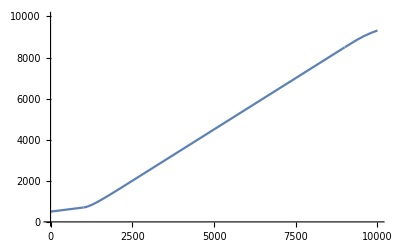

```mathematica
Plot[OptimalCommon[x],{x,0,10000},PlotRange->{{0,10000},{0,10000}}]
```

```mathematica
relData=data;
relData[[All,All,All,2]]=relData[[All,All,All,2]] - relData[[All,All,All,1]];
```

```mathematica
mean=Mean[data[[-50;;]]];
relMean=Mean[relData[[-50;;]]];
```

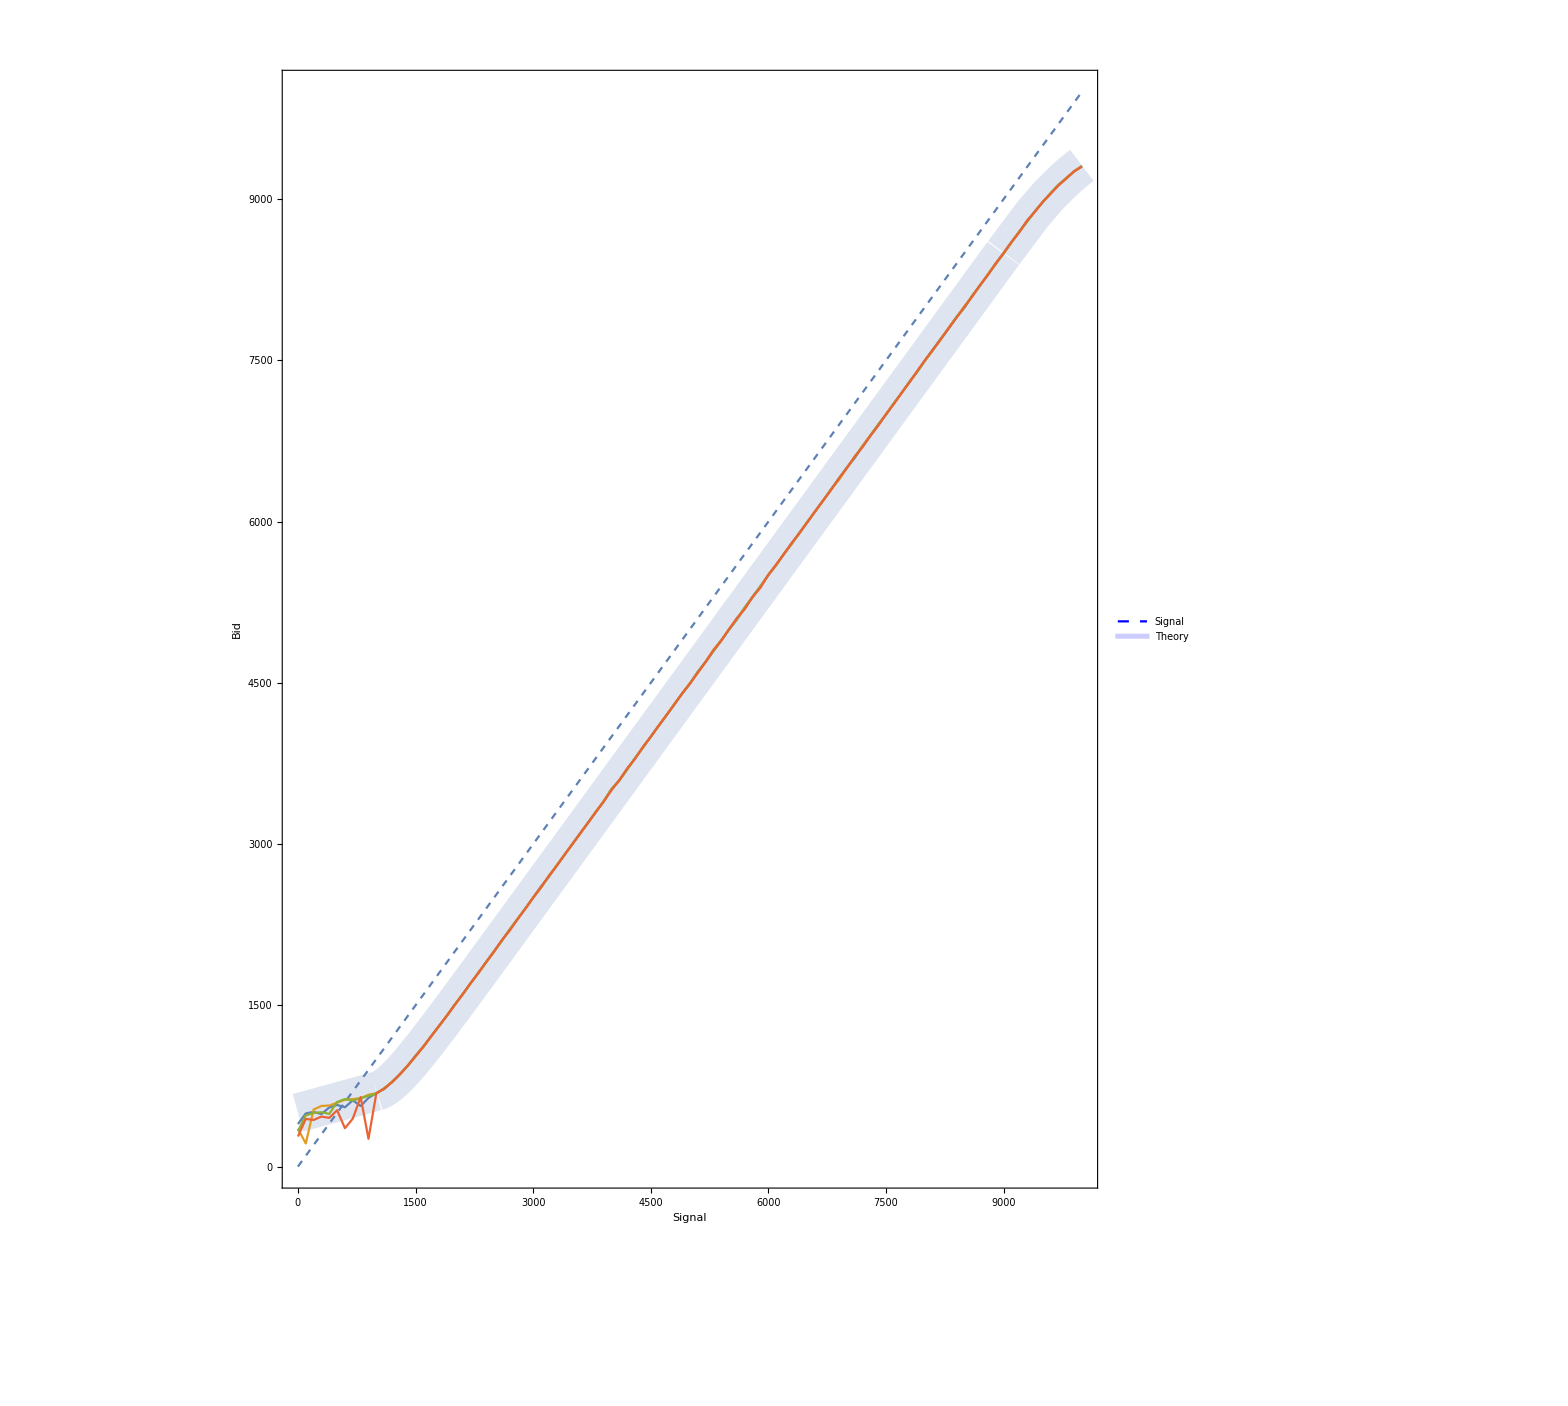

```mathematica
leg=LineLegend[{Directive[Blue,Dashed],Directive[Blue,Thickness[0.02],Opacity[0.20]]},{"Signal","Theory"}];
singleSol=Show[Plot[x,{x,0,10000},PlotRange->{0,10000},PlotStyle->Dashed,PlotLegends->Placed[leg,{Left,Top}]],
Plot[OptimalCommon[v],{v,0,10000},PlotStyle->{Thickness[0.02],Opacity[0.20]}],
ListLinePlot[mean],
Frame->{{True,False},{True,False}},
FrameTicks->{{All,None},{All,None}},
FrameLabel->{{"Bid",None},{"Signal",None}},
LabelStyle->14,
ImageSize->500,
AspectRatio->1,
PlotRangePadding->0
]
```

```mathematica
Export[NotebookDirectory[]<>"text/chapter_4/figures/single_model_bid.jpg",singleSol,ImageResolution->200];
```

```mathematica
xs=data[[1,1,All,1]]
```

{0,100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2100,2200,2300,2400,2500,2600,2700,2800,2900,3000,3100,3200,3300,3400,3500,3600,3700,3800,3900,4000,4100,4200,4300,4400,4500,4600,4700,4800,4900,5000,5100,5200,5300,5400,5500,5600,5700,5800,5900,6000,6100,6200,6300,6400,6500,6600,6700,6800,6900,7000,7100,7200,7300,7400,7500,7600,7700,7800,7900,8000,8100,8200,8300,8400,8500,8600,8700,8800,8900,9000,9100,9200,9300,9400,9500,9600,9700,9800,9900,10000}

```mathematica
D1[xs,#[[All,2]],opts]&/@mean
D2[xs,#[[All,2]],opts]&/@mean
```

{8.46632,8.64177,36.9436,18.1842}

{-1.82031,-2.86167,-11.0448,-5.61462}

```mathematica
opts=N[OptimalCommon/@xs];
```

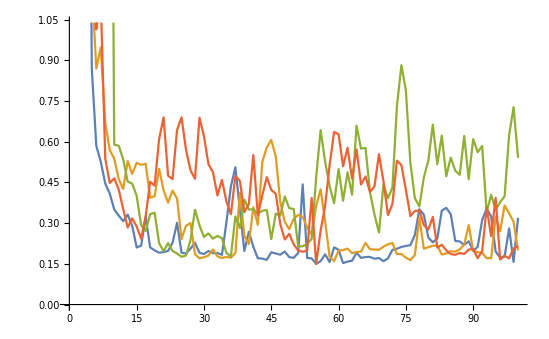

```mathematica
ListLinePlot[Table[D1[xs,#[[i,All,2]],opts]&/@data,{i,1,4}]]
```

```mathematica
Mean[Table[D1[xs,#[[i,All,2]],opts]&/@data,{i,1,4}]]
```

{8.00186,5.39533,3.29313,2.61593,1.73028,1.58423,1.61767,0.817757,1.14087,0.485799,0.450026,0.405124,0.399467,0.383821,0.355365,0.316757,0.359503,0.347636,0.344001,0.38191,0.375154,0.318642,0.326975,0.380933,0.324699,0.30732,0.309872,0.306493,0.335382,0.307465,0.289392,0.2809,0.255643,0.264647,0.262373,0.27971,0.373937,0.374981,0.294537,0.30323,0.368318,0.282321,0.360869,0.390677,0.365823,0.369303,0.296973,0.284758,0.267185,0.265465,0.233469,0.293978,0.219988,0.265737,0.282889,0.375121,0.345344,0.321018,0.345011,0.382066,0.311455,0.357435,0.305148,0.403868,0.346239,0.363047,0.302261,0.284695,0.298346,0.31727,0.278582,0.307784,0.413302,0.448807,0.400067,0.307684,0.294032,0.344928,0.324702,0.316457,0.35817,0.296934,0.343519,0.304307,0.314464,0.276662,0.27607,0.312127,0.297789,0.302542,0.284593,0.320954,0.305486,0.287965,0.315447,0.246503,0.28042,0.352706,0.349045,0.318814}

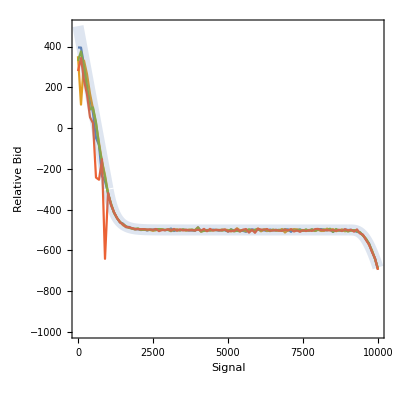

```mathematica
relPlot=Show[ListLinePlot[relMean,PlotRange->{-1000,500}],
Plot[OptimalCommon[s]-s,{s,0,10000},PlotRange->{-1000,500},PlotStyle->{Thickness[0.02],Opacity[0.20]}],
Frame->{{True,False},{True,False}},
FrameTicks->{{All,None},{All,None}},
FrameLabel->{{"Relative Bid",None},{"Signal",None}},
LabelStyle->14,
ImageSize->500,
PlotRangePadding->0,
AspectRatio->1
]
```

```mathematica
Export[NotebookDirectory[]<>"text/chapter_4/figures/single_model_rel.jpg",relPlot,ImageResolution->200];
```

```mathematica
Manipulate[
Show[ListLinePlot[relData[[i]],PlotRange->{-1000,500}],
ImageSize->Large,
Frame->{{True,False},{False,True}},
FrameTicks->{{All,None},{None,All}},
FrameLabel->{{"Relative Bid",None},{None,"Precision"}},
LabelStyle->14
],{i,1,Length[data],1}
]
```

Part::partd: Part specification relData⟦100⟧ is longer than depth of object.

ListLinePlot::lpn: relData⟦100⟧ is not a list of numbers or pairs of numbers.

Show::gtype: ListLinePlot is not a type of graphics.

```mathematica
possDraws=Flatten[Table[{i,j,k,l},{i,1,5},{j,i,5},{k,j,5},{l,k,5}],3];
colors={Red,Lighter@Blue,Darker@Green,Orange};
```

```mathematica
Table[
singleColors=colors[[Position[draws,1][[All,1]]]];
multiColors=Complement[colors,singleColors];
lengthPerParts=Boole[#>1&/@draws]+1;
nParts =Total[lengthPerParts]+1;
data=Import["~/Dropbox/Dissertation/biddingga3/biddingga/output/common_"<>StringJoin[ToString/@draws]<>".csv"];
data=Partition[data,nParts];
data=TakeList[#,Append[lengthPerParts,1]]&/@data;
profits=data[[All,-1,1]];
data=data[[All,;;-2]];
multiData=Select[#,Length[#]>1&]&/@data;
singleData=Select[#,Length[#]==1&][[All,1,1]]&/@data;
multiData=Map[Transpose,multiData,{-3}];
If[Length[multiData]>0,multiData=Last[multiData]];
If[Length[singleData]>0,singleData=Last[singleData]];
{draws,profits[[-1]]}
,{draws,possDraws}
]
```

{{{1,1,1,1},{50.0161,50.0579,50.0161,50.0161}},{{1,1,1,2},{37.7296,37.7296,37.7578,72.0089}},{{1,1,1,3},{31.9841,32.0064,31.9841,83.202}},{{1,1,1,4},{28.8627,28.8627,28.8627,89.7709}},{{1,1,1,5},{26.9612,26.9612,26.9437,93.701}},{{1,1,2,2},{27.5516,27.5707,54.2312,54.2311}},{{1,1,2,3},{22.5646,22.5646,45.0446,63.0138}},{{1,1,2,4},{19.7086,19.7086,39.6264,68.241}},{{1,1,2,5},{17.9312,17.9312,36.2336,71.6872}},{{1,1,3,3},{17.8607,17.872,51.7082,51.7089}},{{1,1,3,4},{15.1774,15.1868,44.8186,55.8513}},{{1,1,3,5},{13.5032,13.495,40.3401,58.6196}},{{1,1,4,4},{12.5818,12.5818,47.9025,47.9054}},{{1,1,4,5},{10.9511,10.9511,42.5923,50.0146}},{{1,1,5,5},{9.36444,9.36444,44.1748,44.1697}},{{1,2,2,2},{20.6118,41.1033,41.1029,41.1052}},{{1,2,2,3},{16.8532,33.847,33.8478,48.6989}},{{1,2,2,4},{14.5897,29.4112,29.4116,53.4663}},{{1,2,2,5},{13.1266,26.5436,26.5433,56.6774}},{{1,2,3,3},{13.6553,27.5044,40.2247,40.2259}},{{1,2,3,4},{11.68,23.5827,34.8265,44.3381}},{{1,2,3,5},{10.3791,20.9936,31.1994,47.1489}},{{1,2,4,4},{9.86738,19.957,38.3151,38.3167}},{{1,2,4,5},{8.65793,17.5271,34.1182,40.6947}},{{1,2,5,5},{7.51115,15.2101,36.1051,36.1003}},{{1,3,3,3},{11.1562,33.253,33.2547,33.2529}},{{1,3,3,4},{9.54181,28.6573,28.6576,37.0129}},{{1,3,3,5},{8.44869,25.5067,25.5067,39.6411}},{{1,3,4,4},{8.13545,24.544,32.0138,32.0133}},{{1,3,4,5},{7.16616,21.6933,28.4778,34.3787}},{{1,3,5,5},{6.26848,19.0148,30.5534,30.5552}},{{1,4,4,4},{6.96229,27.6387,27.6392,27.6388}},{{1,4,4,5},{6.13217,24.5118,24.5109,29.8528}},{{1,4,5,5},{5.39411,21.6604,26.5505,26.5504}},{{1,5,5,5},{4.75337,23.5969,23.5966,23.5974}},{{2,2,2,2},{31.8575,31.858,31.8576,31.8579}},{{2,2,2,3},{26.3958,26.3957,26.3959,38.5784}},{{2,2,2,4},{22.9062,22.9059,22.9062,42.9882}},{{2,2,2,5},{20.5525,20.5531,20.5529,46.0283}},{{2,2,3,3},{21.842,21.8414,32.2352,32.2358}},{{2,2,3,4},{18.8567,18.8566,28.0072,36.1485}},{{2,2,3,5},{16.8023,16.8022,25.0608,38.8967}},{{2,2,4,4},{16.1661,16.1662,31.4328,31.4325}},{{2,2,4,5},{14.2971,14.2972,28.0666,33.8636}},{{2,2,5,5},{12.5469,12.547,30.1951,30.1952}},{{2,3,3,3},{18.2119,27.0422,27.0429,27.0426}},{{2,3,3,4},{15.7542,23.4883,23.4884,30.615}},{{2,3,3,5},{14.0186,20.9624,20.9626,33.1708}},{{2,3,4,4},{13.6141,20.3541,26.7089,26.7088}},{{2,3,4,5},{12.0783,18.0955,23.8587,29.0362}},{{2,3,5,5},{10.6756,16.0147,25.9611,25.9598}},{{2,4,4,4},{11.8064,23.3155,23.3158,23.3152}},{{2,4,4,5},{10.4864,20.8088,20.8084,25.4889}},{{2,4,5,5},{9.30677,18.5317,22.8121,22.8119}},{{2,5,5,5},{8.27819,20.4158,20.4156,20.4154}},{{3,3,3,3},{22.8787,22.879,22.8791,22.8787}},{{3,3,3,4},{19.9427,19.9426,19.9427,26.1631}},{{3,3,3,5},{17.8103,17.8102,17.8103,28.5647}},{{3,3,4,4},{17.4012,17.4009,22.9389,22.9408}},{{3,3,4,5},{15.5297,15.5293,20.5428,25.1554}},{{3,3,5,5},{13.8262,13.8262,22.5677,22.5681}},{{3,4,4,4},{15.2434,20.1632,20.1634,20.1631}},{{3,4,4,5},{13.6254,18.068,18.0679,22.2332}},{{3,4,5,5},{12.1802,16.1818,19.9868,19.9878}},{{3,5,5,5},{10.9121,17.983,17.9831,17.9834}},{{4,4,4,4},{17.797,17.7971,17.7973,17.7965}},{{4,4,4,5},{15.9839,15.984,15.9838,19.7398}},{{4,4,5,5},{14.3692,14.3692,17.7961,17.7964}},{{4,5,5,5},{12.9464,16.0686,16.0685,16.0686}},{{5,5,5,5},{14.5527,14.5527,14.5524,14.5524}}}

```mathematica
draws={2,3,4,5};
```

```mathematica
singleColors=colors[[Position[draws,1][[All,1]]]];
multiColors=Complement[colors,singleColors];
lengthPerParts=Boole[#>1&/@draws]+1;
nParts =Total[lengthPerParts]+1;
data=Import["~/Dropbox/Dissertation/biddingga3/biddingga/output/common_"<>StringJoin[ToString/@draws]<>".csv"];
data=Partition[data,nParts];
data=TakeList[#,Append[lengthPerParts,1]]&/@data;
profits=data[[All,-1,1]];
data=data[[All,;;-2]];
multiData=Select[#,Length[#]>1&]&/@data;
singleData=Select[#,Length[#]==1&][[All,1,1]]&/@data;
multiData=Map[Transpose,multiData,{-3}];
If[Length[multiData]>0,multiData=Last[multiData]];
If[Length[singleData]>0,singleData=Last[singleData]];
```

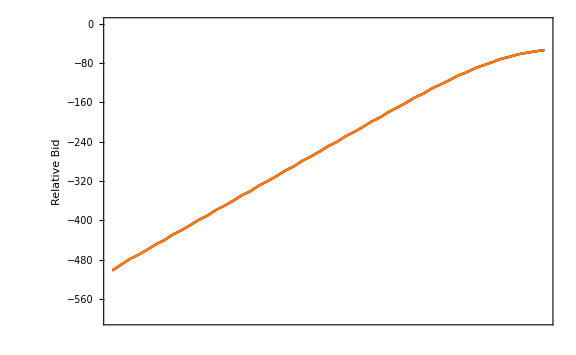

```mathematica
legend=LineLegend[colors,draws,LegendLabel->"Signals",LabelStyle->14,LegendFunction->"Frame",LegendMarkerSize->{30,5}];
Show[
ListLinePlot[multiData,
PlotStyle->multiColors,
PlotRange->{{0,1000},{-600,0}},
PlotLegends->Placed[legend,{Left,Top}]
],
ListPlot[List/@Transpose[{ConstantArray[1000,Length[singleData]],singleData}],
PlotStyle->singleColors,
PlotRange->{{0,1000},{-600,0}}
],
ImageSize->Large,
PlotRange->{{0,1000},{-600,0}},
PlotRangePadding->10,
Frame->{{True,False},{False,True}},
FrameTicks->{{All,None},{None,All}},
FrameLabel->{{"Relative Bid",None},{None,"Precision"}},
LabelStyle->14
]
```

```mathematica
multiData
```

{{{0,-502.016},{20,-490.021},{40,-478.503},{60,-469.905},{80,-459.713},{100,-448.913},{120,-440.099},{140,-428.668},{160,-419.835},{180,-409.874},{200,-398.755},{220,-390.199},{240,-378.665},{260,-369.836},{280,-359.866},{300,-348.732},{320,-340.214},{340,-328.676},{360,-319.83},{380,-309.871},{400,-298.72},{420,-290.223},{440,-278.654},{460,-269.844},{480,-259.875},{500,-248.738},{520,-240.251},{540,-228.682},{560,-219.862},{580,-209.955},{600,-198.948},{620,-190.507},{640,-179.178},{660,-170.331},{680,-160.855},{700,-150.159},{720,-142.209},{740,-131.53},{760,-123.512},{780,-115.006},{800,-105.617},{820,-99.0122},{840,-90.337},{860,-84.2986},{880,-78.0103},{900,-71.4559},{920,-67.2578},{940,-62.1462},{960,-59.0393},{980,-56.282},{1000,-53.6638}},{{0,-501.369},{20,-490.085},{40,-478.501},{60,-469.906},{80,-459.723},{100,-448.915},{120,-440.204},{140,-428.645},{160,-419.859},{180,-409.731},{200,-398.842},{220,-390.197},{240,-378.662},{260,-369.822},{280,-359.874},{300,-348.744},{320,-340.189},{340,-328.686},{360,-319.808},{380,-309.874},{400,-298.721},{420,-290.229},{440,-278.672},{460,-269.837},{480,-259.874},{500,-248.734},{520,-240.196},{540,-228.715},{560,-219.871},{580,-209.939},{600,-198.965},{620,-190.516},{640,-179.152},{660,-170.462},{680,-160.818},{700,-150.079},{720,-142.2},{740,-131.529},{760,-123.549},{780,-114.989},{800,-105.613},{820,-98.9914},{840,-90.3502},{860,-84.2694},{880,-78.1231},{900,-71.4425},{920,-67.2515},{940,-62.1309},{960,-59.048},{980,-56.3067},{1000,-53.5784}},{{0,-501.228},{20,-490.011},{40,-478.53},{60,-469.868},{80,-459.859},{100,-448.828},{120,-440.135},{140,-428.662},{160,-419.826},{180,-409.867},{200,-398.756},{220,-390.195},{240,-378.667},{260,-369.817},{280,-359.884},{300,-348.722},{320,-340.237},{340,-328.668},{360,-319.8},{380,-309.887},{400,-298.721},{420,-290.216},{440,-278.683},{460,-269.82},{480,-259.9},{500,-248.741},{520,-240.23},{540,-228.689},{560,-219.851},{580,-209.99},{600,-198.936},{620,-190.521},{640,-179.223},{660,-170.306},{680,-160.845},{700,-150.161},{720,-142.203},{740,-131.535},{760,-123.548},{780,-114.971},{800,-105.602},{820,-98.9937},{840,-90.3672},{860,-84.2458},{880,-78.1194},{900,-71.435},{920,-67.2786},{940,-62.1413},{960,-59.015},{980,-56.3223},{1000,-53.6655}},{{0,-501.056},{20,-489.946},{40,-478.497},{60,-469.901},{80,-459.715},{100,-448.928},{120,-440.12},{140,-428.646},{160,-419.852},{180,-409.878},{200,-398.749},{220,-390.236},{240,-378.632},{260,-369.824},{280,-359.907},{300,-348.731},{320,-340.202},{340,-328.667},{360,-319.857},{380,-309.874},{400,-298.724},{420,-290.233},{440,-278.668},{460,-269.816},{480,-259.886},{500,-248.741},{520,-240.234},{540,-228.705},{560,-219.861},{580,-209.938},{600,-198.957},{620,-190.515},{640,-179.183},{660,-170.338},{680,-160.845},{700,-150.147},{720,-142.226},{740,-131.504},{760,-123.542},{780,-114.99},{800,-105.616},{820,-99.0138},{840,-90.35},{860,-84.2641},{880,-78.1074},{900,-71.4591},{920,-67.2619},{940,-62.1465},{960,-59.0188},{980,-56.3249},{1000,-53.5872}}}

```mathematica
singleData
```

{}

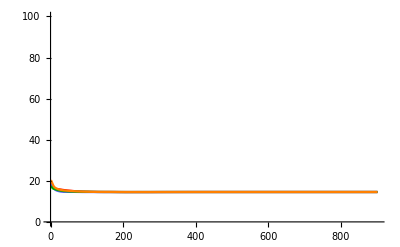

```mathematica
ListLinePlot[Transpose[MovingAverage[profits,100]],PlotRange->{0,100},PlotStyle->colors]
```

```mathematica
Mean[profits[[-100;;]]]
```

{14.5528,14.5528,14.5527,14.5525}

```mathematica
draws={1,2,3,4};
```

```mathematica
plots2=Table[
singleColors=colors[[Position[draws,1][[All,1]]]];
multiColors=Select[colors,!MemberQ[singleColors,#]&];
lengthPerParts=Boole[#>1&/@draws]+1;
nParts =Total[lengthPerParts]+1;
data=Import["~/Dropbox/Dissertation/biddingga3/biddingga/output/common_"<>StringJoin[ToString/@draws]<>".csv"];
data=Partition[data,nParts];
data=TakeList[#,Append[lengthPerParts,1]]&/@data;
profits=data[[All,-1,1]];
data=data[[All,;;-2]];
multiData=Select[#,Length[#]>1&]&/@data;
singleData=Select[#,Length[#]==1&][[All,1,1]]&/@data;
multiData=Map[Transpose,multiData,{-3}];
nMulti=Length[multiColors];

multiDataMin=multiData;
multiDataMin[[All,All,All,2]]=multiDataMin[[All,All,All,2]]+(-500 + multiDataMin[[All,All,All,1]]/2);
multiDataMax=multiData;
multiDataMax[[All,All,All,2]]=multiDataMax[[All,All,All,2]]+(500 - multiDataMax[[All,All,All,1]]/2);

i=-1;
legend=LineLegend[colors,draws,LegendLabel->"Signals",LabelStyle->14,LegendFunction->"Frame",LegendMarkerSize->{30,5}];
plot=Show[
Plot[500-1/2x,{x,0,1000},PlotStyle->Thickness[0.005]],
Plot[-500+1/2x,{x,0,1000},PlotStyle->Thickness[0.005]],
ListLinePlot[If[Length[multiData]>0,Flatten[{multiData[[i]],multiDataMax[[i]],multiDataMin[[i]]},1],multiData],
PlotStyle->Join[multiColors,(Directive[#,Opacity[0]]&/@Flatten[Table[multiColors,2],1])],
Filling->Table[{(j+nMulti)->{{j+2*nMulti},Directive[multiColors[[j]],Opacity[0.05]]}},{j,1,nMulti}],
PlotRange->{{0,1000},{-500,500}},
PlotLegends->Placed[legend,{Right,Top}]
],
ListPlot[If[Length[singleData]>0,List/@Transpose[{ConstantArray[0,Length[singleData[[i]]]],singleData[[i]]}],singleData],
PlotStyle->singleColors,
PlotRange->{{0,1000},{-500,500}}
],
ImageSize->500,
AspectRatio->1,
PlotRange->{{0,1000},{-500,500}},
PlotRangePadding->10,
Frame->{{True,False},{True,False}},
FrameTicks->{{All,None},{All,None}},
FrameLabel->{{"Relative Bid",None},{"Precision",None}},
LabelStyle->14
];
{plot,draws,profits[[-1]]}
,{draws,possDraws}
];
```

Set::shape: Lists {System`ListPlotsDump`plotmarkers$381399,System`ListPlotsDump`filling$381399,System`ListPlotsDump`mesh$381399,System`ListPlotsDump`colorfunction$381399,System`ListPlotsDump`axesorigin$381399,System`ListPlotsDump`plotstyle$381399} and {None,None,Automatic,{0,0},{Directive[PointSize[7/360],RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]]}} are not the same shape.

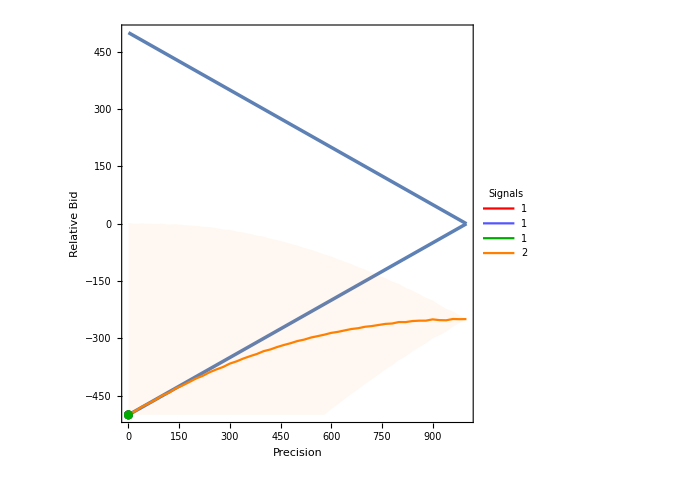
{-Graphics-,{1,1,1,2},{37.7296,37.7296,37.7578,72.0089}}

```mathematica
plots2[[2]]
```

```mathematica
Manipulate[Column[{plots[[i,1]], plots[[i,3]]}],{i,1,Length[plots],1}]
```

```mathematica
Row[{Column[{plots[[40,1]], plots[[21,3]]}],Column[{plots[[22,1]], plots[[22,3]]}]}]
```

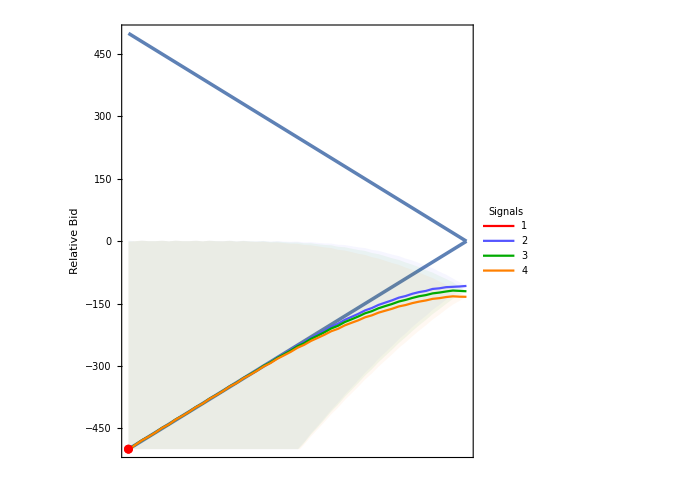
{-Graphics-,{1,2,3,4},{11.68,23.5827,34.8265,44.3381}}

```mathematica
plots2[[21]]
```

```mathematica
Export[NotebookDirectory[]<>"text/chapter_4/figures/2345.jpg",plots2[[50,1]],ImageResolution->150];
```

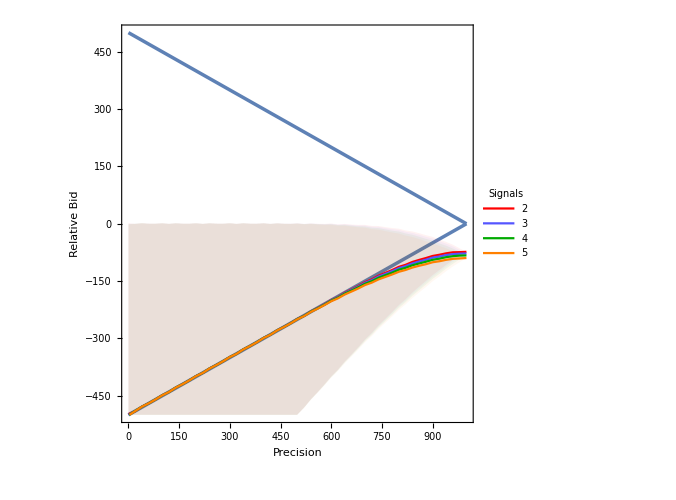

```mathematica
plots2[[50,1]]
```

```mathematica
Dynamic[draws]
```

```mathematica
profs=plots2[[All,3]];
draws=plots2[[All,2]];
```

```mathematica
drawProfs=AssociationThread[draws->profs];
```

```mathematica
allPossDraws=Tuples[Range[5],4];
```

```mathematica
allDrawProfs=AssociationMap[drawProfs[Sort[#]][[Ordering[Ordering[#]]]]&,allPossDraws];
```

```mathematica
cost=10;
```

```mathematica
GetSignalProfits[draws_,allDrawProfs_]:=Module[{altDraw,altProfs,prof},
Table[
If[draws[[i]]==1,
"N/A",
prof=allDrawProfs[draws][[i]];
altDraw=draws;
altDraw[[i]]-=1;
altProfs=allDrawProfs[altDraw];
prof-altProfs[[i]]
]
,{i,1,Length[draws]}
]
];
```

```mathematica
GetNextSignalProfits[draws_,allDrawProfs_]:=Module[{altDraw,altProfs,prof},
Table[
If[draws[[i]]==5,
-100,
prof=allDrawProfs[draws][[i]];
altDraw=draws;
altDraw[[i]]+=1;
altProfs=allDrawProfs[altDraw];
altProfs[[i]]-prof
]
,{i,1,Length[draws]}
]
];
GetPrevSignalProfits[draws_,allDrawProfs_]:=Module[{altDraw,altProfs,prof},
Table[
If[draws[[i]]==1,
-100,
prof=allDrawProfs[draws][[i]];
altDraw=draws;
altDraw[[i]]-=1;
altProfs=allDrawProfs[altDraw];
altProfs[[i]]-prof
]
,{i,1,Length[draws]}
]
];
```

```mathematica
prevSignalProfits=AssociationMap[GetPrevSignalProfits[#,allDrawProfs]&,allPossDraws];
curSignalProfits=AssociationMap[GetSignalProfits[#,allDrawProfs]&,allPossDraws];
nextSignalProfits=AssociationMap[GetNextSignalProfits[#,allDrawProfs]&,allPossDraws];
```

```mathematica
uniqueSignalProfits=KeyTake[nextSignalProfits,Select[possDraws,!MemberQ[#,6]&]];
uniqueSignalProfits2=KeyTake[prevSignalProfits,Select[possDraws,!MemberQ[#,6]&]];
counts=Table[Lookup[#,i,0],{i,1,5}]&/@(Counts/@Keys[uniqueSignalProfits]);
```

```mathematica
profitabilities=Table[
ass=AssociationThread[key->(uniqueSignalProfits[key]-cost)];
ass2=AssociationThread[key->(uniqueSignalProfits2[key]+cost)];
{Lookup[ass,#,0]&/@Range[5],Lookup[ass2,#,0]&/@Range[5]}
,{key,Keys[uniqueSignalProfits]}
];
```

```mathematica
countProfs=Transpose[MapThread[List,{counts,Sign[profitabilities[[All,1]]],Sign[profitabilities[[All,2]]]},2]];
```

```mathematica
Labeled[Labeled[Grid[Map[Item[#[[1]]/.(0->""),Background->Directive[If[#[[1]]==0,White,If[#[[2]]==1,Yellow,If[#[[3]]==1,Red,Green]]],Opacity[0.3]]]&,countProfs,{-2}],Frame->All],{"Grouping",Text[Style["1\n2\n3\n4\n5",12,LineSpacing->{0.6,10}]]},{Top, Left}],{"# of Signals"},{Left}]
```

4 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1 |  |  |  | 2 | 1 | 1 | 1 |  |  |  |  |  |  | 3 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 |  |  |  |  |  |  |  |  |  |  | 4 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | 1 |  |  |  | 1 |  |  | 2 | 1 | 1 |  |  |  |  | 1 |  |  | 2 | 1 | 1 |  |  |  | 3 | 2 | 2 | 1 | 1 | 1 |  |  |  |  |  | 1 |  |  | 2 | 1 | 1 |  |  |  | 3 | 2 | 2 | 1 | 1 | 1 |  |  |  |  | 4 | 3 | 3 | 2 | 2 | 2 | 1 | 1 | 1 | 1 |  |  |  |  | 
 |  |  | 1 |  |  |  | 1 |  |  | 1 |  | 2 | 1 |  |  |  | 1 |  |  | 1 |  | 2 | 1 |  |  | 1 |  | 2 | 1 |  | 3 | 2 | 1 |  |  |  | 1 |  |  | 1 |  | 2 | 1 |  |  | 1 |  | 2 | 1 |  | 3 | 2 | 1 |  |  | 1 |  | 2 | 1 |  | 3 | 2 | 1 |  | 4 | 3 | 2 | 1 | 
 |  |  |  | 1 |  |  |  | 1 |  |  | 1 |  | 1 | 2 |  |  |  | 1 |  |  | 1 |  | 1 | 2 |  |  | 1 |  | 1 | 2 |  | 1 | 2 | 3 |  |  |  | 1 |  |  | 1 |  | 1 | 2 |  |  | 1 |  | 1 | 2 |  | 1 | 2 | 3 |  |  | 1 |  | 1 | 2 |  | 1 | 2 | 3 |  | 1 | 2 | 3 | 4Grouping1
2
3
4
5# of Signals

```mathematica
Export[NotebookDirectory[]<>"valuable_signals.jpg",Labeled[Labeled[Grid[Map[Item[#[[1]]/.(0->""),Background->Directive[{Red,None,Green}[[#[[2]]+2]],Opacity[0.3]]]&,countProfs,{-2}],Frame->All],{"Grouping",Text[Style["1\n2\n3\n4\n5",12,LineSpacing->{0.6,10}]]},{Top, Left}],{"# of Signals"},{Left}],ImageResolution->50,AspectRatio->8]
```

/home/kajames/Dropbox/Dissertation/valuable_signals.jpg

```mathematica
countProfs
```

{{{4,1},{3,1},{3,1},{3,1},{3,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,-1},{1,-1},{1,-1},{1,-1},{1,-1},{1,-1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{1,1},{0,0},{0,0},{0,0},{2,1},{1,1},{1,1},{1,-1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{3,1},{2,1},{2,1},{2,-1},{1,1},{1,1},{1,-1},{1,-1},{1,-1},{1,-1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{4,1},{3,1},{3,1},{3,-1},{2,1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{1,-1},{1,-1},{1,-1},{1,-1},{1,-1},{1,-1},{1,-1},{1,-1},{1,-1},{1,-1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{1,1},{0,0},{0,0},{0,0},{1,1},{0,0},{0,0},{2,-1},{1,-1},{1,-1},{0,0},{0,0},{0,0},{0,0},{1,-1},{0,0},{0,0},{2,-1},{1,-1},{1,-1},{0,0},{0,0},{0,0},{3,-1},{2,-1},{2,-1},{1,-1},{1,-1},{1,-1},{0,0},{0,0},{0,0},{0,0},{0,0},{1,-1},{0,0},{0,0},{2,-1},{1,-1},{1,-1},{0,0},{0,0},{0,0},{3,-1},{2,-1},{2,-1},{1,-1},{1,-1},{1,-1},{0,0},{0,0},{0,0},{0,0},{4,-1},{3,-1},{3,-1},{2,-1},{2,-1},{2,-1},{1,-1},{1,-1},{1,-1},{1,-1},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{1,-1},{0,0},{0,0},{0,0},{1,-1},{0,0},{0,0},{1,-1},{0,0},{2,-1},{1,-1},{0,0},{0,0},{0,0},{1,-1},{0,0},{0,0},{1,-1},{0,0},{2,-1},{1,-1},{0,0},{0,0},{1,-1},{0,0},{2,-1},{1,-1},{0,0},{3,-1},{2,-1},{1,-1},{0,0},{0,0},{0,0},{1,-1},{0,0},{0,0},{1,-1},{0,0},{2,-1},{1,-1},{0,0},{0,0},{1,-1},{0,0},{2,-1},{1,-1},{0,0},{3,-1},{2,-1},{1,-1},{0,0},{0,0},{1,-1},{0,0},{2,-1},{1,-1},{0,0},{3,-1},{2,-1},{1,-1},{0,0},{4,-1},{3,-1},{2,-1},{1,-1},{0,0}},{{0,0},{0,0},{0,0},{0,0},{1,0},{0,0},{0,0},{0,0},{1,0},{0,0},{0,0},{1,0},{0,0},{1,0},{2,0},{0,0},{0,0},{0,0},{1,0},{0,0},{0,0},{1,0},{0,0},{1,0},{2,0},{0,0},{0,0},{1,0},{0,0},{1,0},{2,0},{0,0},{1,0},{2,0},{3,0},{0,0},{0,0},{0,0},{1,0},{0,0},{0,0},{1,0},{0,0},{1,0},{2,0},{0,0},{0,0},{1,0},{0,0},{1,0},{2,0},{0,0},{1,0},{2,0},{3,0},{0,0},{0,0},{1,0},{0,0},{1,0},{2,0},{0,0},{1,0},{2,0},{3,0},{0,0},{1,0},{2,0},{3,0},{4,0}}}

```mathematica
SwatchLegend[{Yellow,Green,Red},{"Desire More","Content","Desire Fewer"}]
```

```mathematica
valuableSignals=Row[{"# of Signals",
Column[{Labeled[Grid[Map[Item[#[[1]]/.(0->""),Background->Directive[If[#[[1]]==0,White,If[#[[2]]==1,Yellow,If[#[[3]]==1,Red,Green]]],Opacity[0.3]]]&,countProfs[[All,1;;35]],{-2}],Frame->All],{"Grouping",Text[Style["1\n2\n3\n4\n5",12,LineSpacing->{0.6,10}]]},{Top, Left}],
Labeled[Grid[Map[Item[#[[1]]/.(0->""),Background->Directive[If[#[[1]]==0,White,If[#[[2]]==1,Yellow,If[#[[3]]==1,Red,Green]]],Opacity[0.3]]]&,countProfs[[All,36;;]],{-2}],Frame->All],{Text[Style["1\n2\n3\n4\n5",12,LineSpacing->{0.6,10}]]},{Left}]}], SwatchLegend[{Yellow,Green,Red},{"Desires More","Contented","Desires Fewer"}]},"   "]
```

# of Signals4 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
 | 1 |  |  |  | 2 | 1 | 1 | 1 |  |  |  |  |  |  | 3 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 |  |  |  |  |  |  |  |  |  | 
 |  | 1 |  |  |  | 1 |  |  | 2 | 1 | 1 |  |  |  |  | 1 |  |  | 2 | 1 | 1 |  |  |  | 3 | 2 | 2 | 1 | 1 | 1 |  |  |  | 
 |  |  | 1 |  |  |  | 1 |  |  | 1 |  | 2 | 1 |  |  |  | 1 |  |  | 1 |  | 2 | 1 |  |  | 1 |  | 2 | 1 |  | 3 | 2 | 1 | 
 |  |  |  | 1 |  |  |  | 1 |  |  | 1 |  | 1 | 2 |  |  |  | 1 |  |  | 1 |  | 1 | 2 |  |  | 1 |  | 1 | 2 |  | 1 | 2 | 3Grouping1
2
3
4
5
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1 |  |  | 2 | 1 | 1 |  |  |  | 3 | 2 | 2 | 1 | 1 | 1 |  |  |  |  | 4 | 3 | 3 | 2 | 2 | 2 | 1 | 1 | 1 | 1 |  |  |  |  | 
 |  | 1 |  |  | 1 |  | 2 | 1 |  |  | 1 |  | 2 | 1 |  | 3 | 2 | 1 |  |  | 1 |  | 2 | 1 |  | 3 | 2 | 1 |  | 4 | 3 | 2 | 1 | 
 |  |  | 1 |  |  | 1 |  | 1 | 2 |  |  | 1 |  | 1 | 2 |  | 1 | 2 | 3 |  |  | 1 |  | 1 | 2 |  | 1 | 2 | 3 |  | 1 | 2 | 3 | 41
2
3
4
5

```mathematica
Export[NotebookDirectory[]<>"text/chapter_4/figures/valuable_signals_"<>ToString[cost]<>".jpg",valuableSignals,ImageResolution->150, AspectRatio->8]
```

/home/kajames/Dropbox/Dissertation/text/chapter_4/figures/valuable_signals_10.jpg

```mathematica
allDrawProfs[{5,3,1,2}]
```

{47.1343,31.1818,10.3623,20.9841}

```mathematica
drawProfs[{1,2,3,5}]
```

{10.3623,20.9841,31.1818,47.1343}

```mathematica
allDrawProfs[{3,4,5,5}]
```

{12.172,16.1725,19.9755,19.9759}

```mathematica
GetSignalProfits[{1,1,1,5},allDrawProfs]
```

{N/A,N/A,N/A,3.9305}

```mathematica
allDrawProfs
```

```mathematica
Manipulate[plots[[k]],{k,1,Length[plots],1}]
```

```mathematica
Manipulate[
Show[
Plot[500-1/2x,{x,0,1000},PlotStyle->Thickness[0.005]],
Plot[-500+1/2x,{x,0,1000},PlotStyle->Thickness[0.005]],
ListLinePlot[If[Length[multiData]>0,Flatten[{multiData[[i]],multiDataMax[[i]],multiDataMin[[i]]},1],multiData],
PlotStyle->Join[multiColors,(Directive[#,Opacity[0]]&/@Flatten[Table[multiColors,2],1])],
Filling->Table[{(j+nMulti)->{{j+2*nMulti},Directive[multiColors[[j]],Opacity[0.05]]}},{j,1,nMulti}],
PlotRange->{{0,1000},{-500,500}},
PlotLegends->Placed[legend,{Right,Top}]
],
ListPlot[If[Length[singleData]>0,List/@Transpose[{ConstantArray[0,Length[singleData[[i]]]],singleData[[i]]}],singleData],
PlotStyle->singleColors,
PlotRange->{{0,1000},{-500,500}}
],
ImageSize->800,
PlotRange->{{0,1000},{-500,500}},
PlotRangePadding->10,
Frame->{{True,False},{False,True}},
FrameTicks->{{All,None},{None,All}},
FrameLabel->{{"Relative Bid",None},{None,"Precision"}},
LabelStyle->14
],{i,1,Length[data],1}]
```

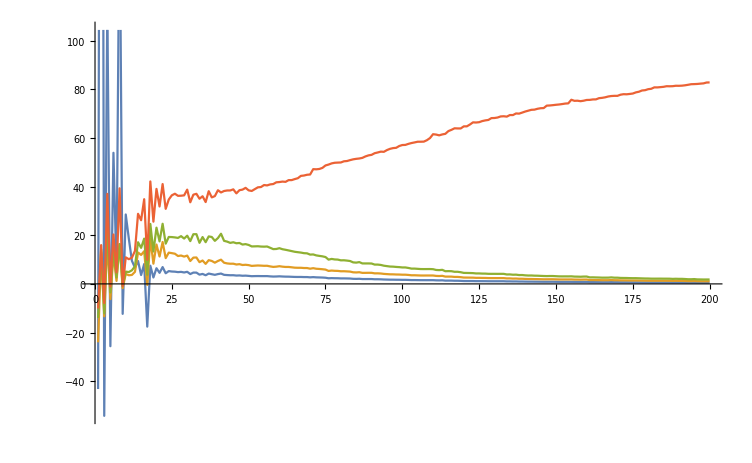

```mathematica
ListLinePlot[Transpose[profits[[1;;200]]]]
```

```mathematica
draws={2,2,2,2};
```

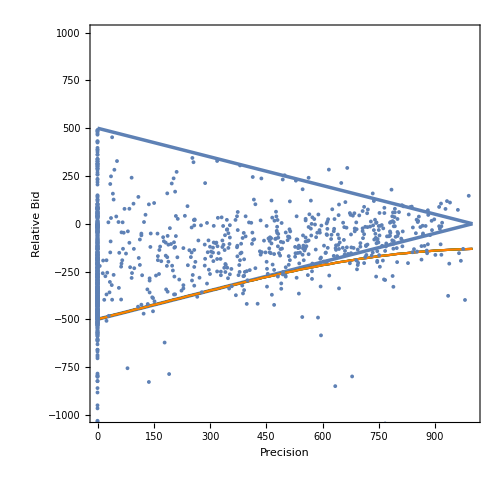

```mathematica
singleColors=colors[[Position[draws,1][[All,1]]]];
multiColors=Select[colors,!MemberQ[singleColors,#]&];
lengthPerParts=Boole[#>1&/@draws]+1;
nParts =Total[lengthPerParts]+1;
data=Import["~/Dropbox/Dissertation/biddingga3/biddingga/output/common_"<>StringJoin[ToString/@draws]<>".csv"];
data=Partition[data,nParts];
data=TakeList[#,Append[lengthPerParts,1]]&/@data;
profits=data[[All,-1,1]];
data=data[[All,;;-2]];
multiData=Select[#,Length[#]>1&]&/@data;
singleData=Select[#,Length[#]==1&][[All,1,1]]&/@data;
multiData=Map[Transpose,multiData,{-3}];
nMulti=Length[multiColors];

multiDataMin=multiData;
multiDataMin[[All,All,All,2]]=multiDataMin[[All,All,All,2]]+(-500 + multiDataMin[[All,All,All,1]]/2);
multiDataMax=multiData;
multiDataMax[[All,All,All,2]]=multiDataMax[[All,All,All,2]]+(500 - multiDataMax[[All,All,All,1]]/2);

i=-1;
legend=LineLegend[colors,draws,LegendLabel->"Signals",LabelStyle->14,LegendFunction->"Frame",LegendMarkerSize->{30,5}];
plot=Show[
Plot[500-1/2x,{x,0,1000},PlotStyle->Thickness[0.005]],
Plot[-500+1/2x,{x,0,1000},PlotStyle->Thickness[0.005]],
ListLinePlot[If[Length[multiData]>0,Flatten[{multiData[[i]],multiDataMax[[i]],multiDataMin[[i]]},1],multiData],
PlotStyle->Join[multiColors,(Directive[#,Opacity[0]]&/@Flatten[Table[multiColors,2],1])],
PlotRange->{{0,1000},{-1000,1000}}
],
ListPlot[If[Length[singleData]>0,List/@Transpose[{ConstantArray[0,Length[singleData[[i]]]],singleData[[i]]}],singleData],
PlotStyle->singleColors,
PlotRange->{{0,1000},{-1000,1000}}
],
ListPlot[Thread[{precs,discounts}]],
ImageSize->500,
PlotRange->{{0,1000},{-1000,1000}},
PlotRangePadding->10,
Frame->{{True,False},{True,False}},
FrameTicks->{{All,None},{All,None}},
FrameLabel->{{"Relative Bid",None},{"Precision",None}},
LabelStyle->14,
AspectRatio->1
]
```

```mathematica
Export[NotebookDirectory[]<>"text/chapter_4/figures/losers_bids.jpg",plot,ImageResolution->150];
```

```mathematica
Dynamic[i]
```

```mathematica
eq=multiData[[-1,1]]
```

{{0,-498.179},{20,-490.422},{40,-478.692},{60,-469.777},{80,-459.851},{100,-448.65},{120,-440.286},{140,-428.698},{160,-419.804},{180,-409.849},{200,-398.653},{220,-390.362},{240,-378.815},{260,-370.011},{280,-360.201},{300,-349.172},{320,-341.037},{340,-329.781},{360,-321.091},{380,-311.67},{400,-301.081},{420,-293.325},{440,-282.79},{460,-274.621},{480,-265.973},{500,-256.205},{520,-249.222},{540,-239.717},{560,-232.547},{580,-225.017},{600,-216.478},{620,-210.539},{640,-202.594},{660,-196.475},{680,-190.489},{700,-183.392},{720,-178.809},{740,-172.457},{760,-167.662},{780,-163.258},{800,-157.841},{820,-154.642},{840,-150.087},{860,-146.69},{880,-144.04},{900,-140.213},{920,-138.449},{940,-135.915},{960,-133.987},{980,-133.037},{1000,-131.42}}

```mathematica
bid3d=Flatten[Table[Table[{precBid[[1]],i,i+precBid[[2]]},{i,-500+precBid[[1]]/2,500-precBid[[1]]/2,5}],{precBid,eq}],1];
```

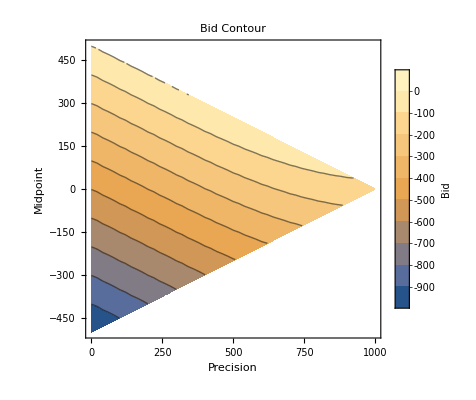

```mathematica
bidContour=ListContourPlot[bid3d,PlotRangePadding->0,FrameLabel->{{"Midpoint",None},{"Precision",None}},PlotLabel->"Bid Contour",PlotLegends->BarLegend[Automatic, LegendLabel->"Bid"]]
```

```mathematica
Export[NotebookDirectory[]<>"bid_contour_2222.jpg",bidContour,ImageResolution->150]
```

/home/kajames/Dropbox/Dissertation/bid_contour_2222.jpg

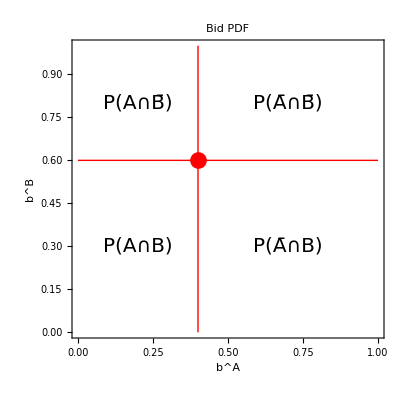

```mathematica
pdfPlot=Show[
ListPlot[{}
,PlotRange->{{0,1},{0,1}}
,AspectRatio->1
,Frame->True
, FrameLabel->{{"b^B",None},{"b^A",None}}
,PlotLabel->"Bid PDF"
],
Graphics[{Red,Line[{{0.4,0},{0.4,1}}]}],
Graphics[{Red,Line[{{0,0.6},{1,0.6}}]}],
Graphics[{Red,PointSize[0.03],Point[ {0.4,0.6}]}],
Graphics[Text[Style["P(A∩B)",20],{0.2,0.3}]],
Graphics[Text[Style["P(A∩B̄)",20],{0.2,0.8}]],
Graphics[Text[Style["P(Ā∩B)",20],{0.7,0.3}]],
Graphics[Text[Style["P(Ā∩B̄)",20],{0.7,0.8}]]
]
```

```mathematica
Export[NotebookDirectory[]<>"text/chapter_3/figures/pdf_plot.jpg",pdfPlot,ImageResolution->200]
```

/home/kajames/Dropbox/Dissertation/text/chapter_3/figures/pdf_plot.jpg

```mathematica
ys=Sort/@RandomReal[{0,1},{2,5}];
```

```mathematica
xs=Range[0,1,1/8]
```

{0,1/8,1/4,3/8,1/2,5/8,3/4,7/8,1}

```mathematica
Export[NotebookDirectory[]<>"sample_composite.jpg",ListLinePlot[{Transpose[{xs[[1;;5]],ys[[1]]}],Transpose[{xs[[5;;]],ys[[2]]}]},Mesh->All,AxesLabel->{"v","b(v)"},PlotLabel->"Sample Composite Bid Strategy",LabelStyle->14],ImageResolution->200]
```

/home/kajames/Dropbox/Dissertation/sample_composite.jpg

```mathematica
true=3400;
epsilon=500;
draws=RandomInteger[{true-epsilon,true+epsilon},3]
```

{3055,3534,2963}

```mathematica
minMax={Max[draws-epsilon],Min[draws+epsilon]}
```

{3034,3463}

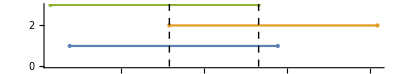

```mathematica
signalSample=Show[
NumberLinePlot[Interval[{#-epsilon,#+epsilon}]&/@draws],
Graphics[{Black,Dashed,Line[{{minMax[[1]],0},{minMax[[1]],4}}]}],
Graphics[{Black,Dashed,Line[{{minMax[[2]],0},{minMax[[2]],4}}]}]
]
```

```mathematica
Export[NotebookDirectory[]<>"signal_sample.jpg",signalSample,ImageResolution->200]
```

/home/kajames/Dropbox/Dissertation/signal_sample.jpg

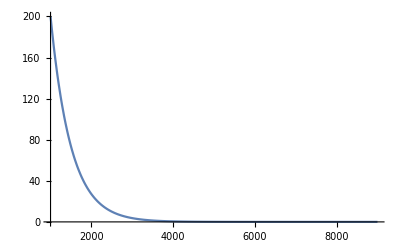

```mathematica
Plot[2*500/5 *E^(-2/(1000)*(x-1000)),{x,1000,9000},PlotRange->All]
```

```mathematica
ys=RandomReal[{0,1},9];
xs=Range[0,1,1/8]
```

{0,1/8,1/4,3/8,1/2,5/8,3/4,7/8,1}

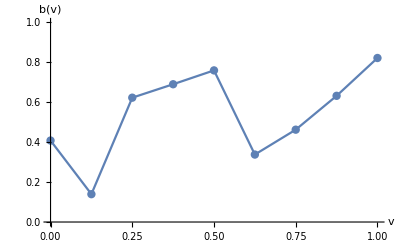

```mathematica
piecewise=ListLinePlot[Transpose[{xs,ys}],PlotRange->{0,1},AxesLabel->{"v","b(v)"},LabelStyle->14,Mesh->All]
```

```mathematica
Export[NotebookDirectory[]<>"text/chapter_2/figures/sample_piecewise.jpg",piecewise,ImageResolution->100];
```

```mathematica
i
```